```mathematica
campo[q_,r_,r1_]:=q (r-r1)/Norm[r-r1]^3
```

```mathematica
potencial[q_,r_,r1_]:=-q /Norm[r-r1]
```

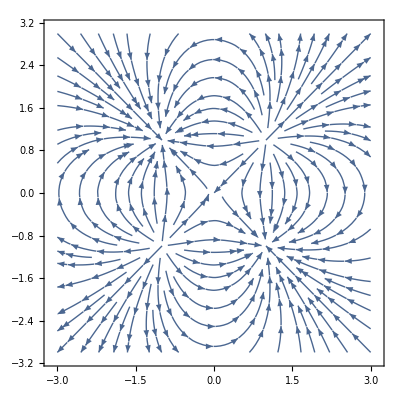

```mathematica
vec=StreamPlot[campo[1,{x,y},{1,1}]+campo[-1,{x,y},{-1,1}]+campo[1,{x,y},{-1,-1}]+campo[-1,{x,y},{1,-1}],{x,-3,3},{y,-3,3}]
```

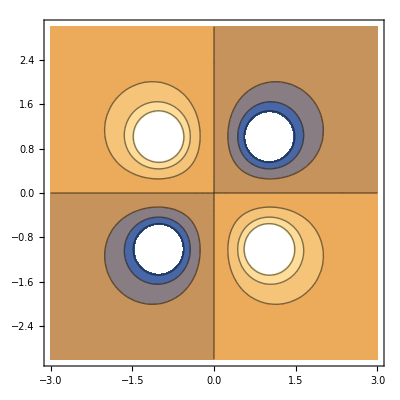

```mathematica
pot=ContourPlot[potencial[1,{x,y},{1,1}]+potencial[-1,{x,y},{-1,1}]+potencial[1,{x,y},{-1,-1}]+potencial[-1,{x,y},{1,-1}],{x,-3,3},{y,-3,3}]
```

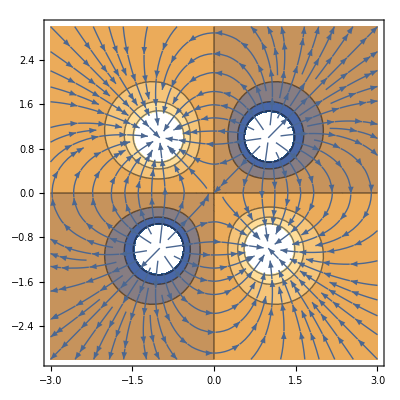

```mathematica
Show[pot,vec]
```

```mathematica
Manipulate[Show[ContourPlot[potencial[q,{x,y},{d,0}]+potencial[-q R/d,{x,y},{R^2/d,0}],{x,-l,l},{y,-l,l}],StreamPlot[campo[q,{x,y},{d,0}]+campo[-q R/d,{x,y},{R^2/d,0}],{x,-l,l},{y,-l,l}],Graphics[Circle[{0,0},R]]],{{q,1},-5,5},{{d,2},0,10},{R,1,10},{{l,5},2,30}]
```

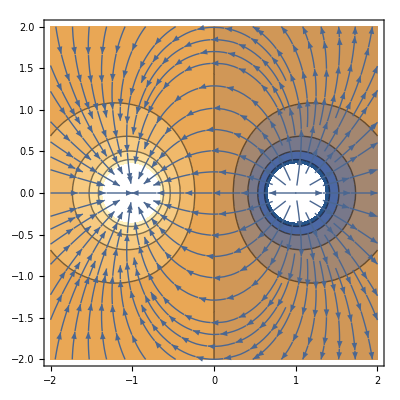

```mathematica
Show[ContourPlot[potencial[1,{x,y},{1,0}]+potencial[-1,{x,y},{-1,0}],{x,-2,2},{y,-2,2}],StreamPlot[campo[1,{x,y},{1,0}]+campo[-1,{x,y},{-1,0}],{x,-2,2},{y,-2,2}]]
```